# DaMaSCUS-CRUST plots

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Constraint plot

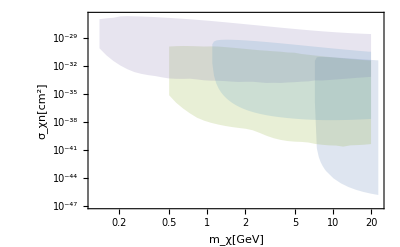

```mathematica
SimID={"XENON1T","CRESST-II","CRESST-2017","DAMIC_2011"};
Experiment={"XENON1T","CRESST-II","CRESST-surface","DAMIC"};
Limits=Table[Import["./results/"<>SimID[[i]]<>"/"<>Experiment[[i]]<>"_Limits.txt","Data"],{i,1,Length[SimID]}];
PlotList={};
For[i=1,i≤Length[SimID],i++,
AppendTo[PlotList,Limits[[i,All,{1,2}]]];
AppendTo[PlotList,Limits[[i,All,{1,3}]]];
]
FillingList=Table[{i->{i+1}},{i,1,Length[PlotList],2}];
ListLogLogPlot[PlotList,Joined->True,PlotStyle->None,Filling->FillingList,Frame->True,FrameLabel->{{"σ_χn[cm^2]",None},{"m_χ[GeV]",None}},GridLines->Automatic]
```